# Plotting of Third order Solution family of differential equations.

## Q1. y’’’-6y’’+11y’-6y=0; y[0]=1, y’[0]=2, y’’[0]=3

```mathematica
sol1=DSolve[{y'''[x]-6*y''[x]+11*y'[x]-6*y[x]==0,y[0]==1,y'[0]==2,y''[0]==3},y[x],x]
```

{{y[x]→-1/2 ⅇ^x (1-4 ⅇ^x+ⅇ^(2 x))}}

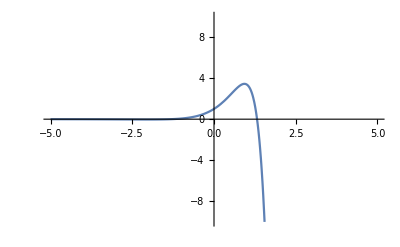

```mathematica
Plot[y[x]/.sol1,{x,-5,5},PlotRange->{-10,10}]
```

## Q2. y’’’-2y’’-y’+2y=0; c1->[2,4,6,7],c2->[1,3,8,9],c3->[2,3,4,5] Use Colors Red Green Blue and Orange

```mathematica
sol2=DSolve[y'''[x]-2 y''[x]-y'[x]+2 y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^x C[2]+ⅇ^(2 x) C[3]}}

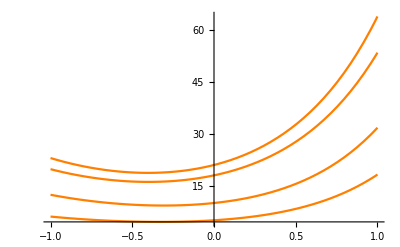

```mathematica
Plot[y[x]/.sol2/.{C[1]->{2,4,6,7},C[2]->{1,3,8,9},C[3]->{2,3,4,5}},{x,-1,1},PlotStyle->{Red,Green,Blue,Orange}]
```

## Q3. y’’’-y’’+100y’-100y=0; y[0]=4,y’[0]=11,y’’[0]=-299

```mathematica
sol3=DSolve[{y'''[x]-y''[x]+100 y'[x]-100y[x]==0,y'[0]==11,y[0]==4,y''[0]==-299},y[x],x]
```

{{y[x]→ⅇ^x+3 Cos[10 x]+Sin[10 x]}}

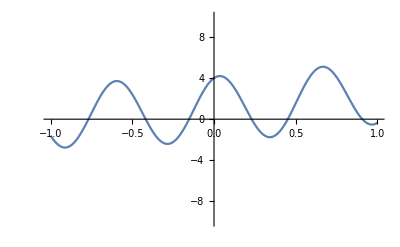

```mathematica
Plot[y[x] /.sol3,{x,-1,1},PlotRange->{-10,10}]
```

## Q4.y’’’-y=0 for {x,-pi,pi}

```mathematica
sol4=DSolve[y'''[x]-y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[3] Sin[(√3 x)/2]}}

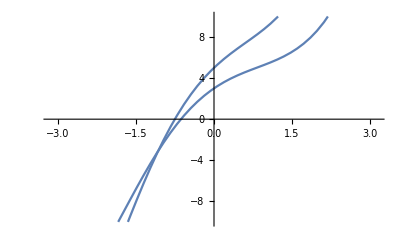

```mathematica
Plot[y[x] /.sol4/.{C[1]->{1,2},C[2]->{2,3},C[3]->{4,5}},{x,-Pi,Pi},PlotRange->{-10,10}]
```

## Q5. y’’’-y’=e^x; c1=[2,3], c2=[1,3], c3=[3,4]

```mathematica
sol5=DSolve[y'''[x]-y'[x]==Exp[x],y[x],x]
```

{{y[x]→ⅇ^x (x/2+1/4 (-3+4 C[1]))-ⅇ^-x C[2]+C[3]}}

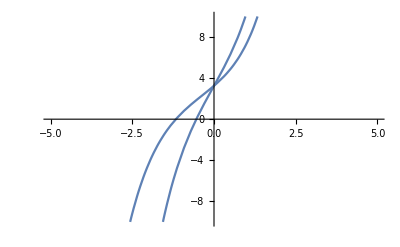

```mathematica
Plot[y[x]/.sol5/.{C[1]->{2,3},C[2]->{1,3},C[3]->{3,4}},{x,-5,5},PlotRange->{-10,10}]
```

## Q6. y’’’[t]+4y’’[t]+7y’-10y=0, x’’’[t]+3.2x’’-4.8x’=0

```mathematica
sol6=DSolve[{y'''[t]+4 y''[t]+7 y'[t]-10 y[t]==0,x'''[t]+3.2 x''[t]-4.8 x'[t]==0},{y[t],x[t]},t]
```

{{y[t]→ⅇ^(t Root0.884Root[-10+7 #1+4 #1^2+#1^3&,1]0.8837178649090873) C[1]+ⅇ^(t Root-2.44-2.31 ⅈRoot[-10+7 #1+4 #1^2+#1^3&,2]-2.4418589324545437) C[2]+ⅇ^(t Root-2.44+2.31 ⅈRoot[-10+7 #1+4 #1^2+#1^3&,3]-2.4418589324545437) C[3],x[t]→-0.231861 ⅇ^(-4.31293 t) C[4]+0.898527 ⅇ^(1.11293 t) C[5]+C[6]}}

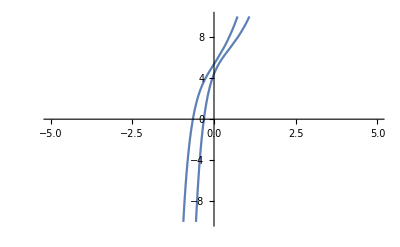

```mathematica
Plot[{y[t],x[t]}/.sol6/.{C[1]->{1,2},C[2]->{3,4},C[3]->{5,6},C[4]->{1,6},C[5]->{4,2},C[6]->{2,4}},{t,-5,5},PlotRange->{-10,10}]
```

## Q7. x’’’[t]+2y’’’[t]-x[t]+y[t]=0,2x’’’[t]+y’’’[t]+2x[t]+y[t]=3e^-t

```mathematica
sol7=DSolve[{x'''[t]+2 y'''[t]-x[t]+y[t]==0,2 x'''[t]+y'''[t]+2 x[t] + y[t]==3 Exp[-t]},{x[t],y[t]},t]
```

{{x[t]→1/1458 ⅇ^(-t-1/2 (3+ⅈ √3) t) (9+9 ⅇ^(t+1/2 (1-ⅈ √3) t)+9 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t+ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅇ^(t+1/2 (1+ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (11+3 ⅈ √3-2 ⅈ √3 t+3 ⅇ^(1/2 (3+ⅈ √3) t) t (8+t)+ⅇ^(ⅈ √3 t) (11-3 ⅈ √3+2 ⅈ √3 t))+1/972 ⅇ^-t (10-5 ⅇ^(t+1/2 (1-ⅈ √3) t)+5 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-5 ⅇ^(t+1/2 (1+ⅈ √3) t)-5 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-4 t+2 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅇ^(t+1/2 (1+ⅈ √3) t) t-2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (12 t+t^2+(4 ⅇ^(-1/2 (3+ⅈ √3) t) (17+5 ⅈ √3-2 ⅈ √3 t))/(-3 ⅈ+√3)^2+(4 ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (17-5 ⅈ √3+2 ⅈ √3 t))/(3 ⅈ+√3)^2)+1/2916 ⅇ^(-t-1/2 (3+ⅈ √3) t) (-2+ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅇ^(t+1/2 (1+ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)) t (5+3 ⅈ √3+4 ⅈ √3 t-6 ⅇ^(1/2 (3+ⅈ √3) t) (-1+t) t+ⅇ^(ⅈ √3 t) (5-3 ⅈ √3-4 ⅈ √3 t))+1/486 ⅇ^-t (-4+2 ⅇ^(t+1/2 (1-ⅈ √3) t)-2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+2 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t+ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅇ^(t+1/2 (1+ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-3 t-t^2-(2 ⅈ ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (-7 ⅈ-√3+4 √3 t))/(3 ⅈ+√3)^2+(2 ⅈ ⅇ^(-1/2 (3+ⅈ √3) t) (7 ⅈ-√3+4 √3 t))/(-3 ⅈ+√3)^2)+1/1458 ⅇ^(-t-1/2 (3+ⅈ √3) t) (2-ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅇ^(t+1/2 (1+ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t+2 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-1+ⅈ (3 ⅈ+√3) t+3 ⅇ^(1/2 (3+ⅈ √3) t) t (1+t)+ⅇ^(ⅈ √3 t) (-1+(-3-ⅈ √3) t))+1/972 ⅇ^-t (-14+7 ⅇ^(t+1/2 (1-ⅈ √3) t)+7 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+7 ⅇ^(t+1/2 (1+ⅈ √3) t)-7 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+4 t+4 ⅇ^(t+1/2 (1-ⅈ √3) t) t+4 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-10 t-t^2+(4 ⅇ^(-1/2 (3+ⅈ √3) t) (13-5 ⅈ √3+(-3-ⅈ √3) t))/(-3 ⅈ+√3)^2+(4 ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (13+5 ⅈ √3+ⅈ (3 ⅈ+√3) t))/(3 ⅈ+√3)^2)+1/27 ⅇ^-t (9+9 ⅇ^(t+1/2 (1-ⅈ √3) t)+9 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t+ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅇ^(t+1/2 (1+ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[1]+1/54 ⅇ^-t (-14+7 ⅇ^(t+1/2 (1-ⅈ √3) t)+7 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+7 ⅇ^(t+1/2 (1+ⅈ √3) t)-7 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+4 t+4 ⅇ^(t+1/2 (1-ⅈ √3) t) t+4 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[2]+1/54 ⅇ^-t (10-5 ⅇ^(t+1/2 (1-ⅈ √3) t)+5 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-5 ⅇ^(t+1/2 (1+ⅈ √3) t)-5 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-4 t+2 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅇ^(t+1/2 (1+ⅈ √3) t) t-2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[3]+1/54 ⅇ^-t (-2+ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅇ^(t+1/2 (1+ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)) t C[4]+1/54 ⅇ^-t (2-ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅇ^(t+1/2 (1+ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t+2 ⅇ^(t+1/2 (1-ⅈ √3) t) t+2 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[5]+1/54 ⅇ^-t (-4+2 ⅇ^(t+1/2 (1-ⅈ √3) t)-2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+2 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t+ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅇ^(t+1/2 (1+ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[6],y[t]→1/729 ⅇ^(-t-1/2 (3+ⅈ √3) t) (2-ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅇ^(t+1/2 (1+ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)) t (11+3 ⅈ √3-2 ⅈ √3 t+3 ⅇ^(1/2 (3+ⅈ √3) t) t (8+t)+ⅇ^(ⅈ √3 t) (11-3 ⅈ √3+2 ⅈ √3 t))+1/243 ⅇ^-t (4-2 ⅇ^(t+1/2 (1-ⅈ √3) t)+2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-2 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t-ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅇ^(t+1/2 (1+ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (12 t+t^2+(4 ⅇ^(-1/2 (3+ⅈ √3) t) (17+5 ⅈ √3-2 ⅈ √3 t))/(-3 ⅈ+√3)^2+(4 ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (17-5 ⅈ √3+2 ⅈ √3 t))/(3 ⅈ+√3)^2)+1/1458 ⅇ^(-t-1/2 (3+ⅈ √3) t) (9+9 ⅇ^(t+1/2 (1-ⅈ √3) t)+9 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t-ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅇ^(t+1/2 (1+ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (5+3 ⅈ √3+4 ⅈ √3 t-6 ⅇ^(1/2 (3+ⅈ √3) t) (-1+t) t+ⅇ^(ⅈ √3 t) (5-3 ⅈ √3-4 ⅈ √3 t))+1/486 ⅇ^-t (26-13 ⅇ^(t+1/2 (1-ⅈ √3) t)+13 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-13 ⅇ^(t+1/2 (1+ⅈ √3) t)-13 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+4 t-2 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅇ^(t+1/2 (1+ⅈ √3) t) t+2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-3 t-t^2-(2 ⅈ ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (-7 ⅈ-√3+4 √3 t))/(3 ⅈ+√3)^2+(2 ⅈ ⅇ^(-1/2 (3+ⅈ √3) t) (7 ⅈ-√3+4 √3 t))/(-3 ⅈ+√3)^2)+1/1458 ⅇ^(-t-1/2 (3+ⅈ √3) t) (-22+11 ⅇ^(t+1/2 (1-ⅈ √3) t)+11 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+11 ⅇ^(t+1/2 (1+ⅈ √3) t)-11 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-4 t-4 ⅇ^(t+1/2 (1-ⅈ √3) t) t-4 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-1+ⅈ (3 ⅈ+√3) t+3 ⅇ^(1/2 (3+ⅈ √3) t) t (1+t)+ⅇ^(ⅈ √3 t) (-1+(-3-ⅈ √3) t))+1/243 ⅇ^-t (-2+ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅇ^(t+1/2 (1+ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t-2 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅇ^(t+1/2 (1+ⅈ √3) t) t) (-10 t-t^2+(4 ⅇ^(-1/2 (3+ⅈ √3) t) (13-5 ⅈ √3+(-3-ⅈ √3) t))/(-3 ⅈ+√3)^2+(4 ⅇ^(1/2 ⅈ (3 ⅈ+√3) t) (13+5 ⅈ √3+ⅈ (3 ⅈ+√3) t))/(3 ⅈ+√3)^2)+2/27 ⅇ^-t (2-ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-ⅇ^(t+1/2 (1+ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)) t C[1]+2/27 ⅇ^-t (-2+ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+ⅇ^(t+1/2 (1+ⅈ √3) t)-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 t-2 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[2]+2/27 ⅇ^-t (4-2 ⅇ^(t+1/2 (1-ⅈ √3) t)+2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-2 ⅇ^(t+1/2 (1+ⅈ √3) t)-2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t-ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅇ^(t+1/2 (1+ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[3]+1/27 ⅇ^-t (9+9 ⅇ^(t+1/2 (1-ⅈ √3) t)+9 ⅇ^(t+1/2 (1+ⅈ √3) t)+2 t-ⅇ^(t+1/2 (1-ⅈ √3) t) t+ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-ⅇ^(t+1/2 (1+ⅈ √3) t) t-ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[4]+1/54 ⅇ^-t (-22+11 ⅇ^(t+1/2 (1-ⅈ √3) t)+11 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)+11 ⅇ^(t+1/2 (1+ⅈ √3) t)-11 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)-4 t-4 ⅇ^(t+1/2 (1-ⅈ √3) t) t-4 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[5]+1/54 ⅇ^-t (26-13 ⅇ^(t+1/2 (1-ⅈ √3) t)+13 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t)-13 ⅇ^(t+1/2 (1+ⅈ √3) t)-13 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t)+4 t-2 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅈ √3 ⅇ^(t+1/2 (1-ⅈ √3) t) t-2 ⅇ^(t+1/2 (1+ⅈ √3) t) t+2 ⅈ √3 ⅇ^(t+1/2 (1+ⅈ √3) t) t) C[6]}}

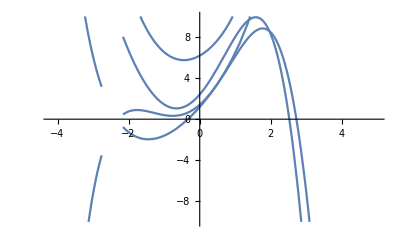

```mathematica
Plot[{y[t],x[t]}/.sol7/.{C[1]->{1,2},C[2]->{3,4},C[3]->{5,6},C[4]->{1,6},C[5]->{4,2},C[6]->{2,4}},{t,-5,5},PlotRange->{-10,10}]
```